# Bifurcación de silla-nodo

## Forma normal:

```mathematica
Manipulate[Plot[r-x^2,{x,-2,2},AxesLabel->{x,OverDot[x]},PlotRange->{Automatic,{-3,3}}],{r,-2,2}]
```

## Diagrama de bifurcación

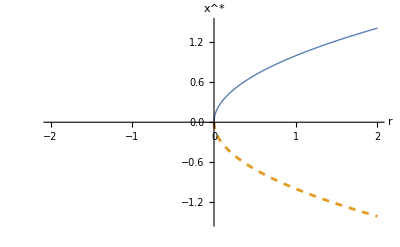

```mathematica
Plot[{Sqrt[r],-Sqrt[r]},{r,0,2},PlotStyle->{Thick,Dashed},AxesLabel->{r,SuperStar[x]},PlotRange->{{-2,2},{-1.5,1.5}}]
```

## Ejemplo I:

```mathematica
Manipulate[Plot[{r-x,Exp[-x]},{x,-2,2},AxesLabel->{x,OverDot[x]},PlotRange->{Automatic,{-3,3}}],{r,0,2}]
```

```mathematica
Manipulate[Plot[r-x-Exp[-x],{x,-2,2},AxesLabel->{x,OverDot[x]},PlotRange->{Automatic,{-3,3}}],{r,0,2}]
```

```mathematica
x/.FindRoot[2-x-Exp[-x]==0,{x,2}]
```

1.84141

```mathematica
branch1=ParallelTable[{r,x/.FindRoot[r-x-Exp[-x]==0,{x,2}]},{r,1,2,0.001}];
branch2=ParallelTable[{r,x/.FindRoot[r-x-Exp[-x]==0,{x,-1}]},{r,1,2,0.001}];
```

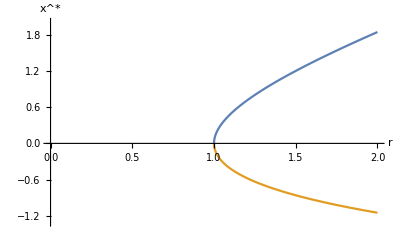

```mathematica
ListPlot[{branch1,branch2},AxesLabel->{r,SuperStar[x]},PlotRange->{{0,2},{-1.3,2}},Joined->True]
```

## Ejemplo II:

### Bifurcación con

```mathematica
Manipulate[Plot[r*x*(1-x)-1,{x,-2,2},AxesLabel->{x,OverDot[x]},PlotRange->{Automatic,{-3,3}}],{r,2,6}]
```

```mathematica
Solve[r*x*(1-x)-1==0,x]
```

{{x→(-√(-4+r) √r+r)/(2 r)},{x→(√(-4+r) √r+r)/(2 r)}}

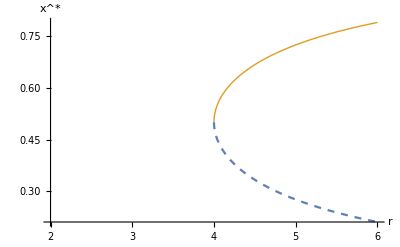

```mathematica
Plot[{(-√(-4+r) √r+r)/(2 r),(√(-4+r) √r+r)/(2 r)},{r,4,6},AxesLabel->{r,SuperStar[x]},PlotStyle->{Dashed,Thick},PlotRange->{{2,6},Automatic}]
```

### Bifurcación con

```mathematica
Manipulate[Plot[x*(1-x)-H,{x,-2,2},AxesLabel->{x,OverDot[x]},PlotRange->{Automatic,{-3,3}}],{H,0,1/2}]
```

```mathematica
Solve[x*(1-x)-H==0,x]
```

{{x→1/2 (1-√(1-4 H))},{x→1/2 (1+√(1-4 H))}}

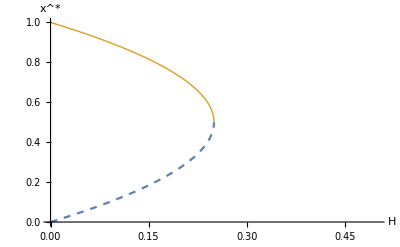

```mathematica
Plot[{1/2 (1-√(1-4 H)),1/2 (1+√(1-4 H))},{H,0,1/4},AxesLabel->{H,SuperStar[x]},PlotStyle->{Dashed,Thick},PlotRange->{{0,1/2},Automatic}]
```

### Bifurcación con

```mathematica
Manipulate[Plot[x*(1-x/k)-1,{x,0,6},AxesLabel->{x,OverDot[x]},PlotRange->{Automatic,{-1,1}}],{k,2,6}]
```

```mathematica
Solve[x*(1-x/k)-1==0,x]
```

{{x→1/2 (-√(-4+k) √k+k)},{x→1/2 (√(-4+k) √k+k)}}

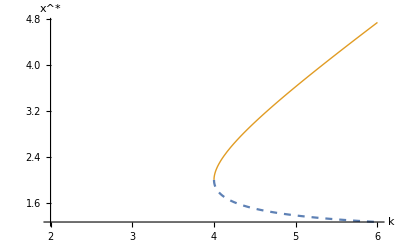

```mathematica
Plot[{1/2 (-√(-4+k) √k+k),1/2 (√(-4+k) √k+k)},{k,4,6},AxesLabel->{k,SuperStar[x]},PlotStyle->{Dashed,Thick},PlotRange->{{2,6},Automatic}]
```

## Ejemplo III:

```mathematica
Manipulate[Plot[{r*Cosh[x],x/2},{x,-4,4},PlotRange->{{-4,4},{-3,3}}],{r,0.1,0.5}]
```

```mathematica
ss1=ParallelTable[{r,x/.FindRoot[r*Cosh[x]-x/2==0,{x,0}]},{r,0.1,0.33137,0.0001}];
ss2=ParallelTable[{r,x/.FindRoot[r*Cosh[x]-x/2==0,{x,10}]},{r,0.1,0.33137,0.0001}];
```

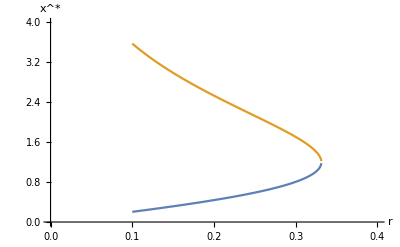

```mathematica
ListPlot[{ss1,ss2},Joined->True,PlotRange->{{0,0.4},{0,4}},AxesLabel->{r,SuperStar[x]}]
```